```mathematica
funTrimList[parList_]:=Module[{listBase,listTrim,inc,l,place},
listBase=Take[parList,3];
listTrim=Partition[Drop[parList,3],2];
l=Length[listTrim];
For[inc=1,inc≤ l,inc++,

If[MemberQ[N[listTrim[[inc]]],0.],
place=False;,
AppendTo[listBase,listTrim[[inc]]];
];

];

Return[Flatten[listBase]];
];


compConstrFun[k_]:=Module[{eqBase,h0eq,i,parBase,eliBase,g0eq,kgeq},
eqBase={h0== h+hd,d0== d+hd,kd== hd/(h*d)};
h0eq={h0,h+hd};
parBase={h0,d0,kd};
eliBase={h,d};
For[i=0,i≤ k,i++,
If[i>0,
g0eq={ToExpression["g0"<>ToString[i]]== ToExpression["g"<>ToString[i]]+ToExpression["hg"<>ToString[i]]};
kgeq={ToExpression["kg"<>ToString[i]]== ToExpression["hg"<>ToString[i]]/(ToExpression["g"<>ToString[i]]*ToExpression["h"])};
AppendTo[eqBase,g0eq[[1]]];
AppendTo[parBase,Symbol["g0"<>ToString@i]];
AppendTo[eliBase,Symbol["g"<>ToString@i]];
AppendTo[eqBase,kgeq[[1]]];
AppendTo[parBase,Symbol["kg"<>ToString@i]];
AppendTo[eliBase,Symbol["hg"<>ToString@i]];
h0eq={h0eq[[1]],h0eq[[2]]+ToExpression["hg"<>ToString[i]]};
eqBase=ReplacePart[eqBase,1-> h0eq[[1]]== h0eq[[2]]];

];

];

Return[{eqBase,parBase,eliBase}]
];

compElimFunHD[parm_]:=compElimFunHD[parm]=Module[{result,sol,brac,l,eliHD},
l=Length[parm];
result=compConstrFun[(l-3)/2];
eliHD=Eliminate[result[[1]]/.Thread[result[[2]]-> parm],result[[3]]];
sol=hd/.NSolve[eliHD,hd];
Return[sol];

];

compResultFunHD[input_]:=compResultFunHD[input]=Module[{result,sol,brac,l,par,posZero,trimPar},
par=N[input];
Off[Select::normal];
l=Length[par];
If[(AllTrue[par,NumericQ]&&OddQ[l]),
If[(par[[1]]==0.||par[[2]]==0.),
sol=0.;,
	If[MemberQ[Drop[par,3],0.],
	trimPar=funTrimList[par];
	sol=compElimFunHD[trimPar];,
	sol=compElimFunHD[par];
	];
];

	result=Select[Re[sol],0.≤#≤par[[1]]&&0.≤#≤par[[2]]&];
	brac=First[result];
,brac="False"];

Return[brac];
];
```

```mathematica
list1={1,2,3,9,89}
AllTrue[par,NumericQ]&&
```

{1,2,3,9,89}

```mathematica
compResultFunHD[list1]
```

0.00830062

```mathematica
list2={1,2,3,0,198,9,89}
compResultFunHD[list2]
```

{1,2,3,0,198,9,89}

0.00830062

```mathematica
list3={1,2,3}
compResultFunHD[list3]
```

{1,2,3}

0.78475

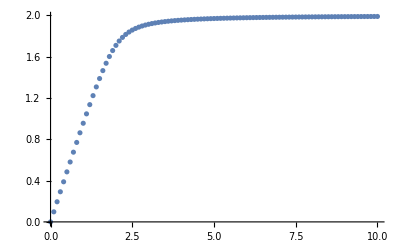

```mathematica
simData=Table[{N[i],compResultFunHD[{i,2,20}]},{i,0,10,0.1}];
%//ListPlot
```

```mathematica
fitsignal=NonlinearModelFit[simData,compElimFunHD[{h0,2,kd}],{{kd,19.}},h0];
```

NonlinearModelFit::eqineq: Constraints in {(0.5 (1.+2. kd+h0 kd+√(-8. h0 kd^2+(-1.+Times[«2»]+Times[«3»])^2)))/kd} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

```mathematica
compElimFunHD[{h0,1,kd,9,8}]
```

{-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)-(0.419974 (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))+1/(-8. kd+kd^2)0.264567 (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3),-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)+((0.209987+0.363708 ⅈ) (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))-1/(-8. kd+kd^2)(0.132283-0.229122 ⅈ) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3),-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)+((0.209987-0.363708 ⅈ) (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))-1/(-8. kd+kd^2)(0.132283+0.229122 ⅈ) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3)}